```mathematica
File
```

```mathematica
vasa=Import["D:\\space\\processing_play\\vasa_1\\data\\tusion_logo.png"]
```

-Graphics-

```mathematica
edges=EdgeDetect[vasa,2,0.07,Method->"Canny"]
```

-Graphics-

```mathematica
edgesData=ImageData[edges]
```

{1}
 |  |  |  |

```mathematica
l={};
valLess[seq_,val_]:=Block[{},Select[ Sort[seq],#<=val&]][[-1]];

For[i=1,i<=Length@edgesData,i++,
(*l = AppendTo[l,Quiet[Check[Position[edgesData[[i]],1]//Flatten//Nearest[#1,Length@edgesData/2,4]&//Append[#1,Length@edgesData]&//Sort//#1[[2]]&,0]]];*)
l = AppendTo[l,Quiet[Check[Position[edgesData[[i]],1]//Flatten//valLess[#1,Length@edgesData/2]&,0]]];
];

Quiet[Check[Position[edgesData[[100]],1]//Flatten//Nearest[#1,1029/2,4]&//Append[#1,500]&//Sort//{#1[[2]]}&,0]]
```

{500}

```mathematica
l
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,514,181,169,164,162,162,163,163,164,164,164,165,165,166,166,166,167,167,168,168,168,169,169,169,170,170,170,171,171,171,172,172,172,173,173,173,174,174,174,174,175,175,175,175,176,176,176,176,177,177,177,177,177,178,178,178,178,178,178,179,179,179,179,179,179,179,179,180,180,180,180,180,180,180,181,181,181,181,181,181,181,181,182,182,182,182,182,182,182,183,183,183,183,183,183,183,184,184,184,184,184,184,184,185,185,185,185,185,185,185,186,186,186,186,186,186,186,187,187,187,187,187,187,188,188,188,188,188,188,189,189,189,189,189,189,190,190,190,190,190,190,191,191,191,191,191,191,192,192,192,192,192,192,193,193,193,193,193,193,194,194,194,194,194,194,195,195,195,195,195,195,196,196,196,196,196,196,196,197,197,197,197,197,197,197,197,198,198,198,198,198,198,198,198,199,199,199,199,199,199,199,199,199,199,199,199,199,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,202,202,202,202,203,203,203,203,204,204,204,205,205,205,206,206,207,207,207,208,208,209,209,210,210,211,211,212,212,213,213,214,214,215,215,216,217,217,218,218,219,220,220,221,221,222,223,223,224,225,225,226,227,227,228,229,230,230,231,232,232,233,234,235,235,236,237,238,239,239,240,241,242,242,243,244,245,246,247,247,248,249,250,251,252,252,253,254,255,256,257,258,258,259,260,261,262,263,264,265,266,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,349,350,351,351,352,352,353,353,354,354,354,355,355,356,356,356,357,357,357,357,358,358,358,358,359,359,359,359,359,359,359,360,360,360,360,360,360,360,360,360,360,360,360,359,359,359,359,359,359,359,358,358,358,358,357,357,357,356,356,355,355,355,354,354,353,352,352,351,351,350,349,348,348,347,346,345,344,343,343,342,341,340,339,338,337,336,335,334,333,332,331,330,329,327,326,325,324,323,322,321,320,318,317,316,315,314,312,311,310,309,308,306,305,304,303,301,300,299,297,296,295,293,292,291,289,288,286,285,283,281,279,277,276,275,275,275,275,275,275,276,276,277,277,278,279,279,280,281,281,282,282,283,284,284,285,285,286,286,286,287,287,287,288,288,288,288,288,288,289,289,289,289,289,289,289,289,289,288,288,288,288,288,288,287,287,287,286,286,286,285,285,284,284,283,282,282,281,280,280,279,278,277,277,276,276,275,275,275,275,276,278,280,281,282,283,284,285,285,286,286,287,287,288,288,288,288,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,289,288,288,288,288,288,288,287,287,287,287,287,286,286,286,285,285,285,284,284,283,283,282,282,281,281,280,280,279,278,278,277,276,276,275,274,273,273,272,271,270,269,269,268,267,266,266,265,264,264,264,263,263,262,262,262,262,261,261,261,261,261,261,261,261,261,261,261,261,261,261,261,261,262,262,262,262,262,262,262,262,262,263,263,263,263,263,263,264,264,264,264,265,265,265,265,266,266,266,266,267,267,268,268,268,269,269,270,270,270,271,271,272,272,273,273,274,275,275,276,276,277,277,278,278,279,279,280,280,281,281,282,283,283,284,284,284,285,285,286,286,287,287,288,288,288,289,289,289,290,290,290,290,291,291,291,291,291,291,291,289,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

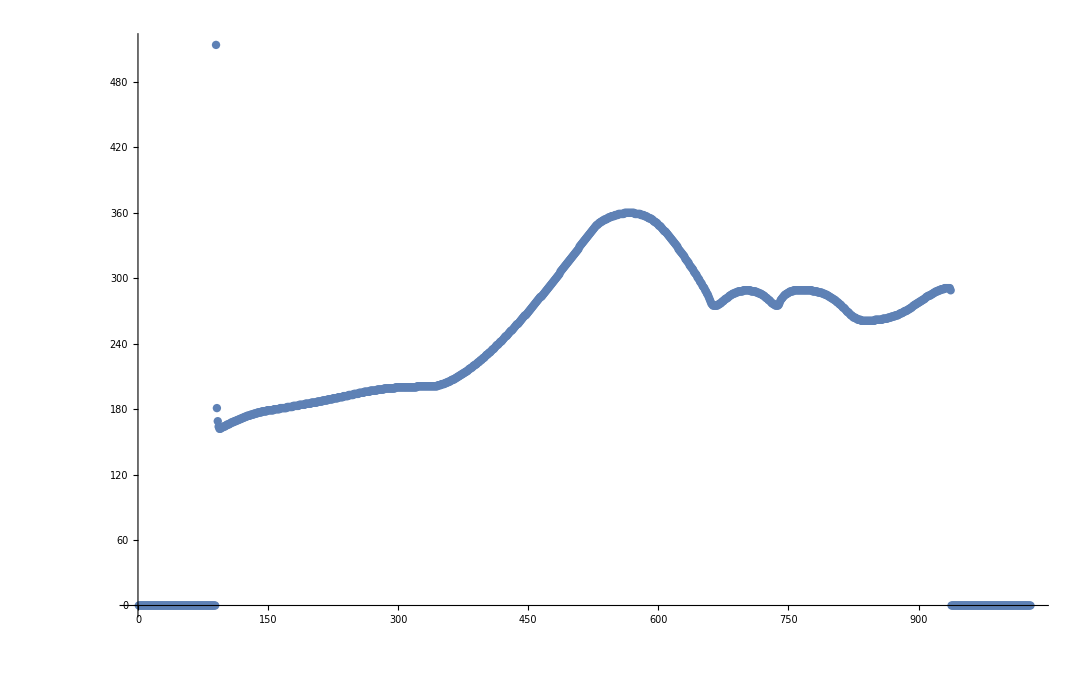

```mathematica
ListPlot[l]
```

```mathematica
Nearest
Quiet
```